```mathematica
xmin=-8; xmax=8;
sol=NDSolve[{D[u[x,t],t]==6u[x,t] D[u[x,t],x]-D[u[x,t],x,x,x],u[x,0]==-2 Sech[x]^2, u[xmin,t]==u[xmax,t]},u,{x,xmin,xmax},{t,-1,1}]//Inactivate;

xmin=-8; xmax=8;
sol=NDSolve[{D[u[x,t],t]==6u[x,t] D[u[x,t],x]-D[u[x,t],x,x,x],u[x,0]==Exp[-x^2], u[xmin,t]==u[xmax,t]},u,{x,xmin,xmax},{t,-1,1}]
```

{{u→InterpolatingFunction[{{…, -8., 8., …}, {-1., 1.}}, <>]}}

```mathematica
Plot3D[u[x,t]/.Flatten[sol],{x,xmin,xmax},{t,-1,1},PlotPoints->50, PlotRange->All,AxesLabel->{"x","t","u"}]
```

-Graphics3D-

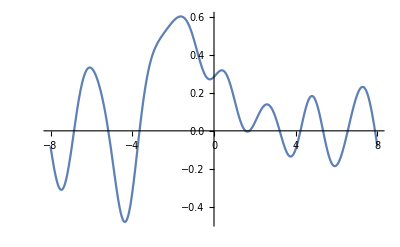

```mathematica
Plot[u[x,0.5]/.Flatten[sol],{x,xmin,xmax},PlotRange->All]
```

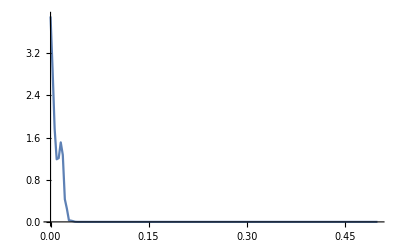

```mathematica
kdvData=Table[u[x,0.5]/.Flatten[sol],{x,xmin,xmax, 0.05}];
Periodogram[kdvData,ScalingFunctions->"Absolute",PlotRange->All]
```

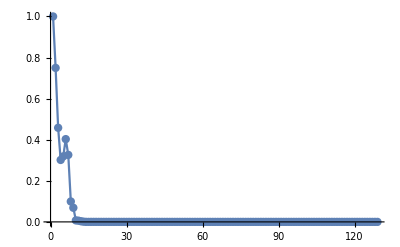

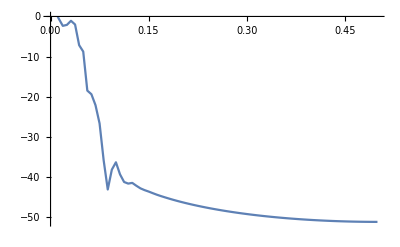

```mathematica
dftKDV=Abs[Fourier[kdvData]]^2/Max[Abs[Fourier[kdvData]]^2];
szKDV=Dimensions[dftKDV][[1]];
dim=Ceiling[0.8szKDV];
dftKDV[[1;;dim]];
(*Periodogram[fpudata,ScalingFunctions->"Absolute",PlotRange->All];*)
ListLinePlot[dftKDV[[1;;dim]],Joined->True,Mesh->All,PlotRange->All]
```